# PLANO DE FOGO PARA BANCADAS Furos de Pequeno Diâmetro

Cálculo do Plano de Fogo para o desmonte de bancadas em minas a céu aberto segundo a metodologia de Jimeno, Jimeno e Carcedo em "Drilling and PBasting of Rocks" para furos de pequeno diâmetro (entre 65 mm e 165 mm).

-Graphics-

Dados de Entrada

```mathematica
TProdTon=500000; (* Produção Desejada Anual, t/ano *)
DensRocha=2.6;(* Densidade da rocha, t/m.b3 *)
TProd=TProdTon/DensRocha;(* Produção em m.b3/ano *)
Frequencia=1; (* Frequencia de detonação, fogo/semana *)
Turno=8;(* Preciso de ajuda, não sei o que é *)
VolFogo=(TProd Frequencia)/52; (* Volume desmontado por fogo, onde 52 é o número de semanas em 1 ano *)
EU=10;(* Espaço útil para trânsito de equipamentos, m *)
H=10;(* Altura da Bancada, m *)
LarguraMax=100;(* Largura máxima disponível *)
nMaxLinhas=5;(* Número Máximo de Linhas *)
β=20;(* Inclinação do Furo, .ba *)
Dcart=75×0.001;(* Diâmetro do Cartucho do Explosivo, m *)
ρ1=0.8;(* Densidade de Explosivo, g/cm^3 *)
ρ2=1.2;(* Densidade do Explosivo, g/cm^3 *)
RCU=80;(* Resistência à Compressão Uniaxial, MPa *)
TamFig=400;(* Tamanho da Figuras *)
Calcular;
```

Parâmetros de Projeto

```mathematica
p={{39,51,35,10,30},{37,47,34,11,35},{35,43,32,12,40},{33,38,30,12,46}};
i=Which[RCU<70,1,RCU≥70&&RCU<120,2,RCU≥120&&RCU<180,3,RCU≥180,4];
PMH=VolFogo/(Turno*7);(*Produção Média por Hora, m^3/h *)
d=Which[RCU<120&&PMH<190,0.065,RCU≥120&&PMH<60,0.065,
RCU<120&&PMH<250,0.089,RCU≥120&&PMH<110,0.089,RCU<120&&PMH<550,0.150,RCU≥120&&PMH<270,0.150
]; (* Diâmetro do furo, m *)
```

Cálculo do Plano de Fogo

```mathematica
B=p⟦i,1⟧d; (* Afastamento, m *)
S=p⟦i,2⟧d ;(* Espaçamento, m *)
T=p⟦i,3⟧d ;(* Comprimento do Tampão, m *)
J=p⟦i,4⟧d; (* Comprimento da Subfuração, m *)
lf=p⟦i,5⟧d; (* Comprimento da Carga de Fundo, m *)
```

```mathematica
L=H/Cos[(β π)/180]+(1-β/100)J;(* Comprimento do furo, m *)
VR=(B S H)/Cos[(β π)/180];(* Volume de Rocha Desmontada, m^3 *)
RA=VR/L;(* Rendimento, m.b3/m *)

qf=(1000 π (1.1 Dcart)^2)/4 ρ2;(* Concentração da Carga de Fundo, kg/m *)
Qf=lf qf;(* Carga de Fundo, kg *)
lc=L-T-lf; (* Comprimento da Carga da Coluna, m *)
qc=(1000 π d^2)/4 ρ1; (* Concentração da Coluna de Carga, kg/m *)
Qc=lc qc;(* Carga da Coluna, kg *)
Qb=Qf+Qc;(* Carga do Furo de Detonação, kg *)
CE=Qb/VR; (* Consumo Específico de Explosivo, kg/m^3 *)
Tf=Ceiling[VolFogo/VR];(* Número de furos totais para atingir produção *)
For[n=1,n≤nMaxLinhas,n++,(* Laço para verificar o número adequado de linhas, iniciando em 1 *)
While[Mod[Tf,n]≠0,(* Enquanto a divisão entre total de furos e número não é inteira *)
Tf+=1(* Incrementa 1 até a divisão ser inteira *)
];
If[Tf*S/n+S<LarguraMax,(* Se a Largura da Bancada é menor que Largura Máxima*)
fpl=Tf/n;(* Número de furos por linha *)
Break[](* Termina o laço inteiro, pois é o valor otimizado *)
];
];
If[n≤nMaxLinhas&&S+fpl*S<LarguraMax,
LB=S+fpl*S;(* Largura da bancada adequada *)
PB=B+n*B+EU; (* Profundidade da bancada adequada *)
,
n=0;
fpl=0;
Print["Não será possível realizar o desmonte"]
];
```

Plano2D

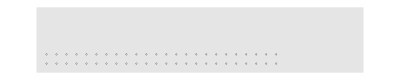

```mathematica
p1=Graphics[{Opacity[.1],Polygon[{{0,0},{LarguraMax,0},{LarguraMax,PB},{0,PB}}]}];
furos=Graphics[Table[Circle[{x,y},d/2],{x,S,LB-S,S},{y,B,n B,B}]];
g1=Show[{furos,p1},ImageSize->TamFig]
```

Plano3D

```mathematica
p1=Graphics3D[{Opacity[.2],
Polygon[{{0,0,0},{LarguraMax,0,0},{LarguraMax,PB,0},{0,PB,0}}]}];
p2=Graphics3D[{Opacity[.2],
Polygon[{{0,0,0},{LarguraMax,0,0},{LarguraMax,-H Tan[β π/180],-H},{0,-H Tan[β π/180],-H}}]}];
p3=Graphics3D[{Opacity[.2],
Polygon[{{0,-H Tan[β π/180],-H},{LarguraMax,-H Tan[β π/180],-H},{LarguraMax,-H Tan[β π/180]-PB/2,-H},{0,-H Tan[β π/180]-PB/2,-H}}]}];
Tampao=Graphics3D[{Red,
Table[Cylinder[{{x,y,0},{x,y-(T) Sin[β π/180],-(T) Cos[β π/180]}},d/2],{x,S,LB-S,S},{y,B,n B,B}]}];
CargaColuna=Graphics3D[{Blue,
Table[Cylinder[{{x,y-(T) Sin[β π/180],-(T) Cos[β π/180]},{x,y-(T+lc) Sin[β π/180],-(T+lc) Cos[β π/180]}},d/2],{x,S,LB-S,S},{y,B,n B,B}]}];
CargaFundo=Graphics3D[{Purple,
Table[Cylinder[{{x,y-(T+lc) Sin[β π/180],-(T+lc) Cos[β π/180]},{x,y-(T+lc+lf) Sin[β π/180],-(T+lc+lf) Cos[β π/180]}},d/2],{x,S,LB-S,S},{y,B,n B,B}]}];
g2=Show[{p1,p2,p3,Tampao,CargaColuna,CargaFundo},Boxed->False,Axes->True,LabelStyle->(FontSize->20),ImageSize->TamFig]
g3=Show[{p1,p2,p3,Tampao,CargaColuna,CargaFundo},ViewPoint->{Infinity,0,0},Boxed->False,Axes->True,LabelStyle->(FontSize->20),ImageSize->TamFig]
```

-Graphics3D-

-Graphics3D-

```mathematica
If[n≠0,
Print["\n- VARIÁVEIS DE PRODUÇÃO -"]
Print["Produção desejada anual: ",TProdTon," ton - ",TProd," m.b3"]
Print["Densidade da rocha: ",DensRocha," t/m.b3"]
Print["Frequência de execução: ",Frequencia, " fogo/semana"]
Print["Volume de rocha desmontada por fogo: ",VolFogo," m.b3"]
Print["Produção média por hora: ",PMH," m^3/h"]
Print["Resistência à compressão uniaxial da rocha: ",RCU," MPa"]
Print["Inclinação do furo: ",β,"°"]
Print["Espaço útil da berma para trânsito de equipamentos: ",EU," m"]
Print["Densidade da carga do explosivo na coluna: ",ρ1," g/cm^3"]
Print["Densidade da carga do explosivo no fundo: ",ρ2," g/cm^3"]
Print["\n- PARÂMETROS DE PROJETO -"]
Print["Largura máxima disponível para execução: ", LarguraMax," m"]
Print["Largura da bancada do projeto: ",LB," m"]
Print["Profundidade da bancada do projeto: ", PB," m"]
Print["Altura da bancada: ",H," m"]
Print["Número total de linhas: ",n"linhas x ",fpl," = ",n*fpl," furos"]
Print["Diâmetro dos furos: ",d," m"]
Print["Afastamento: ",B, " m"]
Print["Espaçamento: ",S," m"]
Print["Comprimento total do furo: ",L," m"]
Print["Comprimento do tampão: ",T," m"]
Print["Comprimento da carga de coluna: ",lc," m"]
Print["Comprimento da carga de fundo: ",lf," m"]
Print["Comprimento da subfuração: ",J," m"]
Print["Volume de Rocha Desmontada por furo: ",VR," m^3"]
Print["Rendimento do Desmonte: ",RA," m^3/m"]
Print["Concentração da Carga de Fundo: ",qf," kg/m"]
Print["Carga de Fundo: ",Qf, " kg"]
Print["Concentração da Carga de Coluna: ",qc, " kg/m"]
Print["Carga de Coluna: ",Qc, " kg"]
Print["Carga total no furo: ",Qb,"kg"]
Print["Carga total de explosivo: ",Qb*Tf," kg"]
Print["Consumo específico: ",CE," kg/m^3"]
];
```

- VARIÁVEIS DE PRODUÇÃO -

Produção desejada anual: 500000 ton - 192308. m.b3

Densidade da rocha: 2.6 t/m.b3

Frequência de execução: 1 fogo/semana

Volume de rocha desmontada por fogo: 3698.22 m.b3

Produção média por hora: 66.0397 m^3/h

Resistência à compressão uniaxial da rocha: 80 MPa

Inclinação do furo: 20°

Espaço útil da berma para trânsito de equipamentos: 10 m

Densidade da carga do explosivo na coluna: 0.8 g/cm^3

Densidade da carga do explosivo no fundo: 1.2 g/cm^3

- PARÂMETROS DE PROJETO -

Largura máxima disponível para execução: 100 m

Largura da bancada do projeto: 76.375 m

Profundidade da bancada do projeto: 17.215 m

Altura da bancada: 10 m

Número total de linhas: 2 linhas x 24 = 48 furos

Diâmetro dos furos: 0.065 m

Afastamento: 2.405 m

Espaçamento: 3.055 m

Comprimento total do furo: 11.2138 m

Comprimento do tampão: 2.21 m

Comprimento da carga de coluna: 6.72878 m

Comprimento da carga de fundo: 2.275 m

Comprimento da subfuração: 0.715 m

Volume de Rocha Desmontada por furo: 78.1881 m^3

Rendimento do Desmonte: 6.9725 m^3/m

Concentração da Carga de Fundo: 6.41474 kg/m

Carga de Fundo: 14.5935 kg

Concentração da Carga de Coluna: 2.65465 kg/m

Carga de Coluna: 17.8625 kg

Carga total no furo: 32.4561kg

Carga total de explosivo: 1557.89 kg

Consumo específico: 0.415102 kg/m^3

```mathematica
Nome="Mina de Calcario";
Export[NotebookDirectory[]<>Nome<>" - Vista de Topo.gif",g1,"GIF"];
Export[NotebookDirectory[]<>Nome<>" - Vista 3D.gif",g2,"GIF"];
Export[NotebookDirectory[]<>Nome<>" - Vista Lateral.gif",g3,"GIF"];

Saida=OpenWrite[NotebookDirectory[]<>Nome<>" - Resultados.txt",CharacterEncoding->"Unicode"];
WriteString[Saida,"RESULTADOS DA SIMULAÇÃO: '",Nome,"' \n"];
WriteString[Saida,"\n\n- VARIÁVEIS DE PRODUÇÃO -\n\n"]
WriteString[Saida,"Produção desejada anual: ",TProdTon," ton - ",TProd," m.b3\n"]
WriteString[Saida,"Densidade da rocha: ",DensRocha," t/m.b3\n"]
WriteString[Saida,"Frequência de desmonte: ",Frequencia," fogo/semana\n"]
WriteString[Saida,"Volume desmontado necessário por fogo: ", VolFogo," m.b3\n"]
WriteString[Saida,"Produção média por hora: ",PMH," m.b3/h\n"]
WriteString[Saida,"Resistência à compressão uniaxial da rocha: ",RCU," MPa\n"]
WriteString[Saida,"Inclinação do furo: ",β,"°\n"]
WriteString[Saida,"Espaço útil da berma para trânsito de equipamentos: ",EU," m\n"]
WriteString[Saida,"Densidade da carga do explosivo na coluna: ",ρ1," g/cm.b3\n"]
WriteString[Saida,"Densidade da carga do explosivo no fundo: ",ρ2," g/cm.b3\n"]
WriteString[Saida,"\n- PARÂMETROS DE PROJETO -\n\n"]
WriteString[Saida,"Largura máxima disponível para execução: ",LarguraMax," m\n"]
WriteString[Saida,"Largura da bancada: ",LB," m\n"]
WriteString[Saida,"Profundidade da bancada: ", PB," m\n"]
WriteString[Saida,"Altura da bancada: ",H," m\n"]
WriteString[Saida,"Número total de linhas: ",n"linhas x ",fpl," = ",n*fpl," furos\n"]
WriteString[Saida,"Diâmetro dos furos: ",d," m\n"]
WriteString[Saida,"Afastamento: ",B, " m\n"]
WriteString[Saida,"Espaçamento: ",S," m\n"]
WriteString[Saida,"Comprimento total do furo: ",L," m\n"]
WriteString[Saida,"Comprimento do tampão: ",T," m\n"]
WriteString[Saida,"Comprimento da carga de coluna: ",lc," m\n"]
WriteString[Saida,"Comprimento da carga de fundo: ",lf," m\n"]
WriteString[Saida,"Comprimento da subfuração: ",J," m\n"]
WriteString[Saida,"Volume de Rocha Desmontada por furo: ",VR," m.b3\n"]
WriteString[Saida,"Volume Total de Rocha Desmontada: ",VR*Tf," m.b3\n"]
WriteString[Saida,"Rendimento do Desmonte: ",RA," m.b3/m\n"]
WriteString[Saida,"Concentração da Carga de Fundo: ",qf," kg/m\n"]
WriteString[Saida,"Carga de Fundo: ",Qf, " kg\n"]
WriteString[Saida,"Concentração da Carga de Coluna: ",qc, " kg/m\n"]
WriteString[Saida,"Carga de Coluna: ",Qc, " kg\n"]
WriteString[Saida,"Carga total no furo: ",Qb,"kg\n"]
WriteString[Saida,"Carga total de explosivo: ", Qb*Tf,"kg\n"]
WriteString[Saida,"Consumo específico: ",CE," kg/m.b3\n"]
Close[Saida];
```